{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6,(-1+x) x^7,(-1+x) x^8,(-1+x) x^9,(-1+x) x^10}

{{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},{0.183367,0.142924,0.106036,0.0802587,0.0624182,0.0497726,0.040554,0.0336553,0.0283717,0.0242425},{0.10959,0.106036,0.0897825,0.074323,0.0616773,0.0516651,0.0437564,0.0374626,0.032401,0.0282843},{0.0727024,0.0802587,0.074323,0.0656456,0.0572207,0.049817,0.0435232,0.0382285,0.0337788,0.0300274},{0.0516873,0.0624182,0.0616773,0.0572207,0.0518372,0.0465536,0.041725,0.0374418,0.0336904,0.0304202},{0.0386087,0.0497726,0.0516651,0.049817,0.0465536,0.0428905,0.0392733,0.0358882,0.0328011,0.0300222},{0.0299313,0.040554,0.0437564,0.0435232,0.041725,0.0392733,0.0366208,0.0339916,0.0314928,0.0291702},{0.0238873,0.0336553,0.0374626,0.0382285,0.0374418,0.0358882,0.0339916,0.031983,0.0299872,0.02807},{0.0195139,0.0283717,0.032401,0.0337788,0.0336904,0.0328011,0.0314928,0.0299872,0.028414,0.0268485},{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}}

{-0.083325,-0.0499917,-0.033325,-0.0238012,-0.0178488,-0.0138806,-0.0111028,-0.00908258,-0.00756743,-0.00640193}

{-0.0937095,-0.496347,0.40126}

Dot::dotsh: Tensors {-0.0937095,-0.496347,0.40126} and {-0.0000204282,-4.17318×10^-10,-8.52521×10^-15,-1.74158×10^-19,-3.5578×10^-24,-7.26807×10^-29,-1.48476×10^-33,-3.03316×10^-38,-6.19631×10^-43,-1.26582×10^-47} have incompatible shapes.

Dot::dotsh: Tensors {-0.0937095,-0.496347,0.40126} and {-0.0200113,-0.000408802,-8.35125×10^-6,-1.70604×10^-7,-3.4852×10^-9,-7.11978×10^-11,-1.45447×10^-12,-2.97128×10^-14,-6.06991×10^-16,-1.24×10^-17} have incompatible shapes.

Dot::dotsh: Tensors {-0.0937095,-0.496347,0.40126} and {-0.0391691,-0.00159954,-0.00006532,-2.66746×10^-6,-1.0893×10^-7,-4.44836×10^-9,-1.81657×10^-10,-7.41826×10^-12,-3.02938×10^-13,-1.2371×10^-14} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

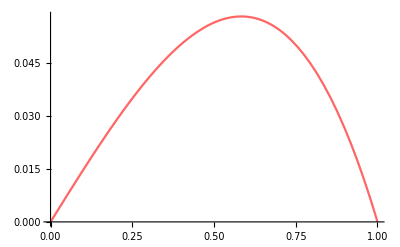

-Graphics-

```mathematica
Tn[f_,{a_,b_,m_}]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,10}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,100],{j,10},{n,10}]
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,100],{j,1,10}]
W=LinearSolve[K1,F1]
Uh[x_]:=W.ϕ
G1=Plot[Uh1[x],{x,0,1},ImageSize->400,AxesStyle->Black]
G2=Plot[x-Sinh[x]/Sinh[1],{x,0,1},PlotStyle->{Red,Opacity[0.6]}]
G3=Show[G2,G1,PlotRange->All,ImageSize->400,AxesStyle->Black]
```

```mathematica
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,100],{j,10},{n,10}]
```

{{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},{0.183367,0.142924,0.106036,0.0802587,0.0624182,0.0497726,0.040554,0.0336553,0.0283717,0.0242425},{0.10959,0.106036,0.0897825,0.074323,0.0616773,0.0516651,0.0437564,0.0374626,0.032401,0.0282843},{0.0727024,0.0802587,0.074323,0.0656456,0.0572207,0.049817,0.0435232,0.0382285,0.0337788,0.0300274},{0.0516873,0.0624182,0.0616773,0.0572207,0.0518372,0.0465536,0.041725,0.0374418,0.0336904,0.0304202},{0.0386087,0.0497726,0.0516651,0.049817,0.0465536,0.0428905,0.0392733,0.0358882,0.0328011,0.0300222},{0.0299313,0.040554,0.0437564,0.0435232,0.041725,0.0392733,0.0366208,0.0339916,0.0314928,0.0291702},{0.0238873,0.0336553,0.0374626,0.0382285,0.0374418,0.0358882,0.0339916,0.031983,0.0299872,0.02807},{0.0195139,0.0283717,0.032401,0.0337788,0.0336904,0.0328011,0.0314928,0.0299872,0.028414,0.0268485},{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}}

```mathematica
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,100],{j,1,10}]
```

{-0.083325,-0.0499917,-0.033325,-0.0238012,-0.0178488,-0.0138806,-0.0111028,-0.00908258,-0.00756743,-0.00640193}

```mathematica
W=LinearSolve[K,F]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},«8»,{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}} may contain significant numerical errors.

{-0.143975,-0.286041,1.01723,-0.88268,-21.7595,114.301,-263.753,322.231,-202.953,51.9334}

```mathematica
Uh1[x_]:=W.ϕ
```

```mathematica
Uh1[x]
```

Dot::dotsh: Tensors {-0.0937095,-0.496347,0.40126} and {(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6,(-1+x) x^7,(-1+x) x^8,(-1+x) x^9,(-1+x) x^10} have incompatible shapes.

{-0.0937095,-0.496347,0.40126}.{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6,(-1+x) x^7,(-1+x) x^8,(-1+x) x^9,(-1+x) x^10}

```mathematica
K//MatrixForm
```

(0.366733 | 0.183367 | 0.10959 | 0.0727024 | 0.0516873 | 0.0386087 | 0.0299313 | 0.0238873 | 0.0195139 | 0.0162505
0.183367 | 0.142924 | 0.106036 | 0.0802587 | 0.0624182 | 0.0497726 | 0.040554 | 0.0336553 | 0.0283717 | 0.0242425
0.10959 | 0.106036 | 0.0897825 | 0.074323 | 0.0616773 | 0.0516651 | 0.0437564 | 0.0374626 | 0.032401 | 0.0282843
0.0727024 | 0.0802587 | 0.074323 | 0.0656456 | 0.0572207 | 0.049817 | 0.0435232 | 0.0382285 | 0.0337788 | 0.0300274
0.0516873 | 0.0624182 | 0.0616773 | 0.0572207 | 0.0518372 | 0.0465536 | 0.041725 | 0.0374418 | 0.0336904 | 0.0304202
0.0386087 | 0.0497726 | 0.0516651 | 0.049817 | 0.0465536 | 0.0428905 | 0.0392733 | 0.0358882 | 0.0328011 | 0.0300222
0.0299313 | 0.040554 | 0.0437564 | 0.0435232 | 0.041725 | 0.0392733 | 0.0366208 | 0.0339916 | 0.0314928 | 0.0291702
0.0238873 | 0.0336553 | 0.0374626 | 0.0382285 | 0.0374418 | 0.0358882 | 0.0339916 | 0.031983 | 0.0299872 | 0.02807
0.0195139 | 0.0283717 | 0.032401 | 0.0337788 | 0.0336904 | 0.0328011 | 0.0314928 | 0.0299872 | 0.028414 | 0.0268485
0.0162505 | 0.0242425 | 0.0282843 | 0.0300274 | 0.0304202 | 0.0300222 | 0.0291702 | 0.02807 | 0.0268485 | 0.0255837)

```mathematica
F//MatrixForm
```

(-0.083325
-0.0499917
-0.033325
-0.0238012
-0.0178488
-0.0138806
-0.0111028
-0.00908258
-0.00756743
-0.00640193)

```mathematica
W=LinearSolve[K,F]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},«8»,{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}} may contain significant numerical errors.

{-0.143975,-0.286041,1.01723,-0.88268,-21.7595,114.301,-263.753,322.231,-202.953,51.9334}

```mathematica
Uh1[x_]:=W.ϕ
```

```mathematica
Uh1[x]
```

-0.143975 (-1+x) x-0.286041 (-1+x) x^2+1.01723 (-1+x) x^3-0.88268 (-1+x) x^4-21.7595 (-1+x) x^5+114.301 (-1+x) x^6-263.753 (-1+x) x^7+322.231 (-1+x) x^8-202.953 (-1+x) x^9+51.9334 (-1+x) x^10

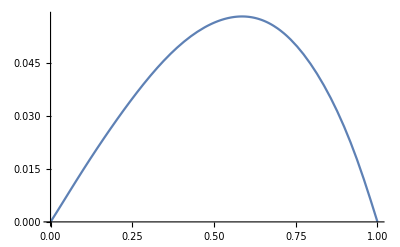

-Graphics-

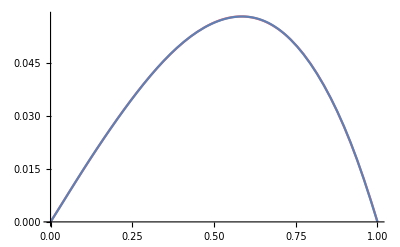

```mathematica
G1=Plot[Uh1[x],{x,0,1},ImageSize->400,AxesStyle->Black]
G2=Plot[x-Sinh[x]/Sinh[1],{x,0,1},PlotStyle->{Red,Opacity[0.6]}]
G3=Show[G2,G1,PlotRange->All,ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["L2_3b_400.png",G3]
```

L2_3b_400.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["L2_3b_400.png"]]]
```

```mathematica
Table[Integrate[D[ϕ[[i]],x]*D[ϕ[[j]],x]+ϕ[[i]]*ϕ[[j]],{x,0,1}],{i,3},{j,3}]-Table[i*j/(i+j-1)-((1+i)j+(1+j)*i)/(i+j)+(1+(1+i)(1+j))/(i+j+1)-2/(i+j+2)+1/(i+j+3),{i,3},{j,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}